```mathematica
x[t_] = x0 Cos[Subscript[ω, 0] t]+v0/Subscript[ω, 0] Sin[Subscript[ω, 0] t];
```

```mathematica
Simplify[x''[t]==-Subscript[ω, 0]^2 x[t]]
```

True

```mathematica
x[0]
```

x0

```mathematica
x'[0]
```

v0

```mathematica
Remove["Global`*"]
```

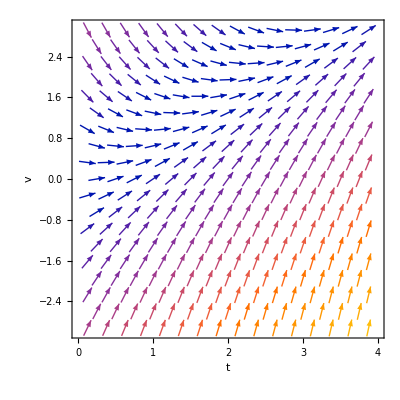

```mathematica
f[t_,v_]=-v+t;
VectorPlot[{1,f[t,v]}, {t,0,4},{v,-3,3},Axes->False, Frame->{{True,False},{True,False}},FrameLabel->{{"v",None},{"t",None}},FrameTicks->All]
```

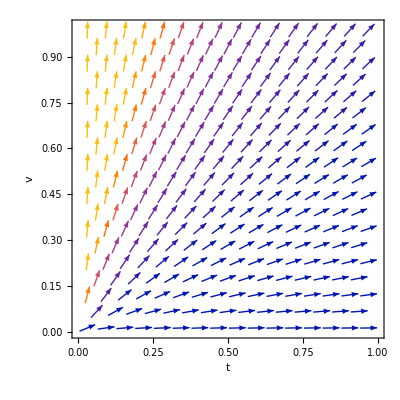

```mathematica
f[t_,v_]=v/t;
VectorPlot[{1,f[t,v]}, {t,0,1},{v,0,1},Axes->False, Frame->{{True,False},{True,False}},FrameLabel->{{"v",None},{"t",None}},FrameTicks->All]
```

```mathematica
Remove["Global`*"]
```

```mathematica
DSolve[x''[t]-t*x[t]==0,x[t],t]
```

{{x[t]→AiryAi[t] C[1]+AiryBi[t] C[2]}}

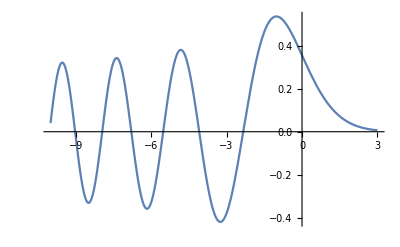

```mathematica
Plot[AiryAi[x],{x,-10,3}]
```

```mathematica
DSolve[x'[t]==t/(x[t]+t)^2,x[t],t]
```

DSolve[x'[t]==t/(t+x[t])^2,x[t],t]

```mathematica
ToFileName[$UserBaseDirectory,"Applications"]
```

/Users/almuravtsev/Library/Mathematica/Applications

```mathematica
Remove["Global`*"]
```

```mathematica
NDSolve[{x'[t]==t/(x[t]+t)^2,x[0]==1},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
x[t]/.%[[1]]
```

InterpolatingFunction[…][t]

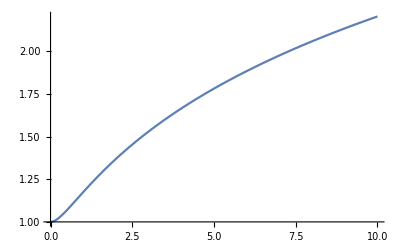

```mathematica
Plot[%,{t,0,10}]
```

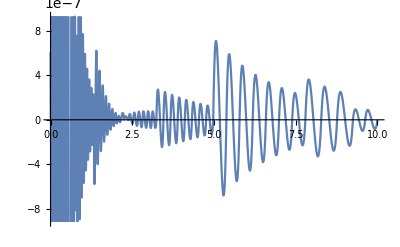

```mathematica
x[t_]=%%;
error[t_]=x'[t]-t/(x[t]+t)^2;
Plot[error[t],{t,0,10}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
Clear[x];
NDSolve[{x''[t]==-x[t],x[0]==1,x'[0]==0},x[t],{t,0,30}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
x[t]/.%[[1]]
```

InterpolatingFunction[…][t]

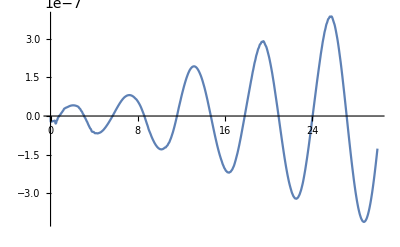

```mathematica
Plot[%-Cos[t],{t,0,30}]
```

```mathematica
xsol[t_]=x[t]/.NDSolve[{x''[t]==-x[t],x[0]==1,x'[0]==0},x[t],{t,0,30},AccuracyGoal->13,PrecisionGoal->13][[1]];
```

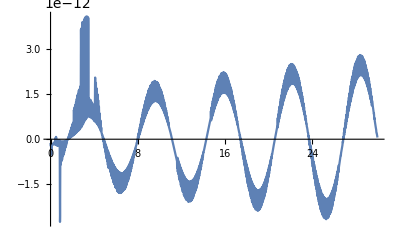

```mathematica
Plot[xsol[t]-Cos[t],{t,0,30}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
z={x[t],v[t]}/.NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-Sin[x[t]-2 t],x[0]==-0.5,v[0]==0},{x[t],v[t]},{t,0,50}][[1]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
z0=Table[{-0.5+10^-5 (2 Random[]-1),10^-5 (2 Random[]-1)},{m,1,40}];
```

```mathematica
Δz[t_]=Table[Sqrt[({x[t],v[t]}-z).({x[t],v[t]}-z)]/.NDSolve[{x'[t]==v[t],v'[t]==-Sin[x[t]]-Sin[x[t]-2 t],x[0]==z0 [[m,1]],v[0]==z0[[m,2]]},{x[t],v[t]},{t,0,50}][[1]],{m,1,40}];
```

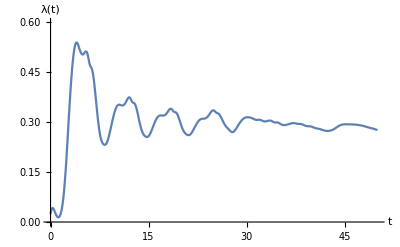

```mathematica
λ[t_]=1/40 Sum[Log[Δz[t][[n]]/Δz[0][[n]]],{n,1,40}]/t;
Plot[λ[t],{t,0,50},PlotRange->{0,0.6},AxesLabel->{"t","λ(t)"}]
```

```mathematica
Remove["Global`*"]
```

```mathematica
t[n_]:=n Δt;
v[n_]:=v[n-1]+Δt f[t[n-1],v[n-1]];
v[0]:=v0
```

```mathematica
v[0.5]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+Δt f[t[0.5-1],v[0.5-1]]

```mathematica
Clear[v]
```

```mathematica
t[n_]:=n Δt;
v[n_]:=v[n-1]+Δt *f[t[n-1],v[n-1]]/;
n>0 && n ϵ Integers;
v[0]:=v0;
```

```mathematica
v[0.5]
```

v[0.5]

```mathematica
v[n_]:=(v[n]=v[n-1]+Δt f[t[n-1],v[n-1]])/;n>0 && n ϵ Integers;
```

```mathematica
t[n_]:=n Δt;
v[n_]:=(v[n]=v[n-1]+Δt f[t[n-1],v[n-1]]) /; n>0 && n ϵ Integers;
v[0]:=v0;
```

```mathematica
Δt = 0.2;
f[t_,v_]=t-v;
v0=0;
```

```mathematica
solution = Table[{t[n], v[n]},{n,0,4/Δt}]
```

{{0.,0},{0.2,v[1]},{0.4,v[2]},{0.6,v[3]},{0.8,v[4]},{1.,v[5]},{1.2,v[6]},{1.4,v[7]},{1.6,v[8]},{1.8,v[9]},{2.,v[10]},{2.2,v[11]},{2.4,v[12]},{2.6,v[13]},{2.8,v[14]},{3.,v[15]},{3.2,v[16]},{3.4,v[17]},{3.6,v[18]},{3.8,v[19]},{4.,v[20]}}

```mathematica
Flatten[solution]
```

{0.,0,0.2,v[1],0.4,v[2],0.6,v[3],0.8,v[4],1.,v[5],1.2,v[6],1.4,v[7],1.6,v[8],1.8,v[9],2.,v[10],2.2,v[11],2.4,v[12],2.6,v[13],2.8,v[14],3.,v[15],3.2,v[16],3.4,v[17],3.6,v[18],3.8,v[19],4.,v[20]}

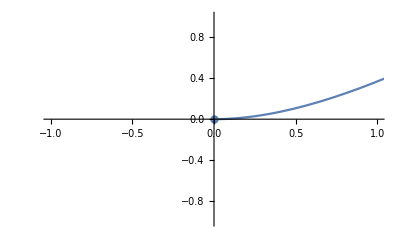

```mathematica
a=ListPlot[solution,PlotStyle->PointSize[0.015],DisplayFunction->Identity];
b=Plot[E^-t+t-1,{t,0,4},DisplayFunction->Identity];
Show[a,b,DisplayFunction->$DisplayFunction]
```

```mathematica
vEuler[t_]=Interpolation[solution][t]
```

InterpolatingFunction[…][t]

```mathematica
vExact[t_]=E^-t+t-1;
pl=Plot[vEuler[t]-vExact[t],{t,0,4}]
```

-Graphics-

```mathematica
Eulersol[v0_,time_,Δt_]:=Module[{t,v,solution},
t[n_]:=n Δt;
v[n_]:=(v[n]=v[n-1]+Δt f[t[n-1],v[n-1]])/;n>0 && n ϵ Integers;
v[0]:=v0;
solution=Table[{t[n],v[n]},{n,0,time/Δt }];
vEuler[t_]=Interpolation[solution][t];]
```

```mathematica
Eulersol[0,4,0.1];
p2=Plot[vEuler[t]-vExact[t],{t,0,4},DisplayFunction->Identity];
Eulersol[0,4,0.05];
p3=Plot[vEuler[t]-vExact[t],{t,0,4},DisplayFunction->Identity];
Show[pl,p2,p3,DisplayFunction->$DisplayFunction,PlotLabel->"Error"]
```

-Graphics-